# Lab #3

## Craig Fox

Clear initial definitions

```mathematica
Remove["Global`*"]
```

Equation

```mathematica
solvedθdt = Solve[((1/2)*m*(l^2)*(dθdt^2))+(m*g*l*(1-Cos[θ])) == m*g*l*(1-Cos[θ0]), dθdt]
```

{{dθdt→-(√2 √(g Cos[θ]-g Cos[θ0]))/(√l)},{dθdt→(√2 √(g Cos[θ]-g Cos[θ0]))/(√l)}}

```mathematica
dt = 1/(dθdt/.solvedθdt[[2]])
```

(√l)/(√2 √(g Cos[θ]-g Cos[θ0]))

```mathematica
T = 4*Integrate[dt, {θ, 0, θ0}, Assumptions->{θ0 > 0,θ0 <π, l > 0, g>0, θ>0, θ<π}]
```

4 √(l/g) EllipticK[Sin[θ0/2]^2]

Plot of Period vs θ

```mathematica
toplot = T/(2π*Sqrt[l/g])
```

(2 EllipticK[Sin[θ0/2]^2])/π

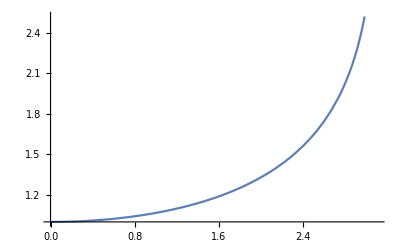

```mathematica
Plot[toplot, {θ0, 0, .99*π}]
```

The period for θ0 is infinity

Put values for l and g. Create a table of the numerical values of the period when you set θ0.

```mathematica
l = 1;
g = 9.81;
θ0Range = Range[.1,3.1,.1];
numericalSolution = Table[(4*NIntegrate[dt,{θ, 0, θ0}]/(2π*Sqrt[l/g])),{θ0,.1,3.1,.1}]
analyticalSolution = Table[toplot,{θ0,.1,3.1,.1}];
```

{1.00063,1.00251,1.00565,1.01009,1.01585,1.02298,1.03151,1.04153,1.05311,1.06633,1.08132,1.09821,1.11715,1.13833,1.16197,1.18834,1.21778,1.25067,1.2875,1.3289,1.37566,1.42879,1.48966,1.56016,1.64298,1.74217,1.86426,2.0208,2.23551,2.57123,3.3485}

Comparison of Numerical vs Analytical Values

```mathematica
Grid[Transpose[{Prepend[θ0Range, "θ0 Values"], Prepend[numericalSolution, "Numerical Values"], Prepend[analyticalSolution, "Analytical Values"]}], Frame->All]
```

θ0 Values | Numerical Values | Analytical Values
0.1 | 1.00063 | 1.00063
0.2 | 1.00251 | 1.00251
0.3 | 1.00565 | 1.00565
0.4 | 1.01009 | 1.01009
0.5 | 1.01585 | 1.01585
0.6 | 1.02298 | 1.02298
0.7 | 1.03151 | 1.03151
0.8 | 1.04153 | 1.04153
0.9 | 1.05311 | 1.05311
1. | 1.06633 | 1.06633
1.1 | 1.08132 | 1.08132
1.2 | 1.09821 | 1.09821
1.3 | 1.11715 | 1.11715
1.4 | 1.13833 | 1.13833
1.5 | 1.16197 | 1.16197
1.6 | 1.18834 | 1.18834
1.7 | 1.21778 | 1.21778
1.8 | 1.25067 | 1.25067
1.9 | 1.2875 | 1.2875
2. | 1.3289 | 1.3289
2.1 | 1.37566 | 1.37566
2.2 | 1.42879 | 1.42879
2.3 | 1.48966 | 1.48966
2.4 | 1.56016 | 1.56016
2.5 | 1.64298 | 1.64298
2.6 | 1.74217 | 1.74217
2.7 | 1.86426 | 1.86426
2.8 | 2.0208 | 2.0208
2.9 | 2.23551 | 2.23551
3. | 2.57123 | 2.57123
3.1 | 3.3485 | 3.3485

Alternative Solution found using Sin[θ0/2]=Au where A=Sin[θ0/2]

```mathematica
Tθ0 = (2/π)Integrate[1/(Sqrt[1-u^2]*Sqrt[1-(A^2)(u^2)]), {u,0,1}]
```

ConditionalExpression[(2 EllipticK[A^2])/π, Re[A^2]≤1||A^2∉ℝ]

Shows that alternative solution is also correct and equal to earlier solutions

```mathematica
A = Sin[θ0/2];
u = Sin[θ/2]/A;
substitutionSolution = Table[Tθ0,{θ0,.1,3.1,.1}];
Grid[Transpose[{Prepend[θ0Range, "θ0 Values"], Prepend[numericalSolution, "Numerical Values"], Prepend[analyticalSolution, "Analytical Values"], Prepend[substitutionSolution, "Substitution Solution Values"]}], Frame->All]
```

θ0 Values | Numerical Values | Analytical Values | Substitution Solution Values
0.1 | 1.00063 | 1.00063 | 1.00063
0.2 | 1.00251 | 1.00251 | 1.00251
0.3 | 1.00565 | 1.00565 | 1.00565
0.4 | 1.01009 | 1.01009 | 1.01009
0.5 | 1.01585 | 1.01585 | 1.01585
0.6 | 1.02298 | 1.02298 | 1.02298
0.7 | 1.03151 | 1.03151 | 1.03151
0.8 | 1.04153 | 1.04153 | 1.04153
0.9 | 1.05311 | 1.05311 | 1.05311
1. | 1.06633 | 1.06633 | 1.06633
1.1 | 1.08132 | 1.08132 | 1.08132
1.2 | 1.09821 | 1.09821 | 1.09821
1.3 | 1.11715 | 1.11715 | 1.11715
1.4 | 1.13833 | 1.13833 | 1.13833
1.5 | 1.16197 | 1.16197 | 1.16197
1.6 | 1.18834 | 1.18834 | 1.18834
1.7 | 1.21778 | 1.21778 | 1.21778
1.8 | 1.25067 | 1.25067 | 1.25067
1.9 | 1.2875 | 1.2875 | 1.2875
2. | 1.3289 | 1.3289 | 1.3289
2.1 | 1.37566 | 1.37566 | 1.37566
2.2 | 1.42879 | 1.42879 | 1.42879
2.3 | 1.48966 | 1.48966 | 1.48966
2.4 | 1.56016 | 1.56016 | 1.56016
2.5 | 1.64298 | 1.64298 | 1.64298
2.6 | 1.74217 | 1.74217 | 1.74217
2.7 | 1.86426 | 1.86426 | 1.86426
2.8 | 2.0208 | 2.0208 | 2.0208
2.9 | 2.23551 | 2.23551 | 2.23551
3. | 2.57123 | 2.57123 | 2.57123
3.1 | 3.3485 | 3.3485 | 3.3485

Series expansion of T(θ0) to the first nonzero order

```mathematica
Series[Tθ0,{θ0,0,2}]
seriesExpansion = 1 + ((θ0^2)/16);
```

ConditionalExpression[1+θ0^2/16+O[θ0]^3, !(Sin[θ0/2]^2∈ℝ&&Re[Sin[θ0/2]^2]>1)]

Looking at the graphs below, 1 is a excellent approximation while θ0 is less than 1.

```mathematica
seriesExpansionApproximation = Table[seriesExpansion,{θ0,.1,3.1,.1}];
Grid[Transpose[{Prepend[θ0Range, "θ0 Values"], Prepend[numericalSolution, "Numerical Values"], Prepend[analyticalSolution, "Series Approximation"]}], Frame->All]
```

θ0 Values | Numerical Values | Series Approximation
0.1 | 1.00063 | 1.00063
0.2 | 1.00251 | 1.00251
0.3 | 1.00565 | 1.00565
0.4 | 1.01009 | 1.01009
0.5 | 1.01585 | 1.01585
0.6 | 1.02298 | 1.02298
0.7 | 1.03151 | 1.03151
0.8 | 1.04153 | 1.04153
0.9 | 1.05311 | 1.05311
1. | 1.06633 | 1.06633
1.1 | 1.08132 | 1.08132
1.2 | 1.09821 | 1.09821
1.3 | 1.11715 | 1.11715
1.4 | 1.13833 | 1.13833
1.5 | 1.16197 | 1.16197
1.6 | 1.18834 | 1.18834
1.7 | 1.21778 | 1.21778
1.8 | 1.25067 | 1.25067
1.9 | 1.2875 | 1.2875
2. | 1.3289 | 1.3289
2.1 | 1.37566 | 1.37566
2.2 | 1.42879 | 1.42879
2.3 | 1.48966 | 1.48966
2.4 | 1.56016 | 1.56016
2.5 | 1.64298 | 1.64298
2.6 | 1.74217 | 1.74217
2.7 | 1.86426 | 1.86426
2.8 | 2.0208 | 2.0208
2.9 | 2.23551 | 2.23551
3. | 2.57123 | 2.57123
3.1 | 3.3485 | 3.3485

Comparison of actual values (blue) vs series expansion estimate (orange)

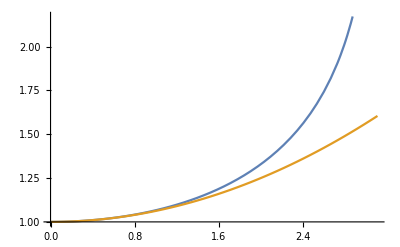

```mathematica
Plot[{toplot, seriesExpansion}, {θ0, 0, .99*π}]
```